```mathematica
Planar=GraphData["Planar"];
```

```mathematica
PC=Select[Planar,GraphData[#,"Connected"]&];
PCC=Select[PC,GraphData[#,"EdgeConnectivity"]≥2&];
```

```mathematica
For[i=1,i≤20,i++,Print[GraphData[PCC[[i]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

```mathematica
GraphData[PC[[1]],"EdgeConnectivity"]
```

2

```mathematica
Complement[Sort[#]&/@GraphData[PC[[2]],"FaceIndices"],{ConvexHull[GraphData[PC[[2]],"VertexCoordinates"]]//Sort}]
```

{{1,5,6}}

```mathematica
(*Graphics for Rose-Hulman Presentation*)
(*Graphic 1- A nice box spline - this is in the file BoxSpline*)
```

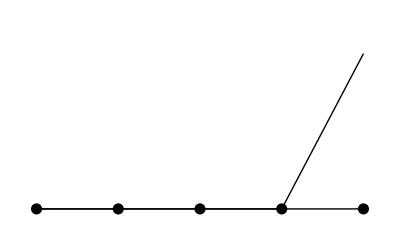

```mathematica
(*Piecewise linear Graphics in one variable*)
Int=Graphics[{PointSize[.02],Point[{#,0}&/@{-2,-1,0,1,2}],Line[{#,0}&/@{-2,-1,0,1,2}]},PlotRange->{-.1,.1}];
f=Interpolation[{{-2,.1},{-1,.6},{0,.6},{1,1.1},{2,.6}}];
g1=Interpolation[{{-2,.1},{-1,.6},{0,.6}},InterpolationOrder->2];
g2=Interpolation[{{0,.6},{1,1.1},{2,.6}},InterpolationOrder->2];
InterPlot=Plot[f[x],{x,-2,2},Axes->False,PlotRange->{-.1,1.2},PlotStyle->{Thick,Red}];
QuadPlot=Plot[Piecewise[{{g1[x],-2≤x<0},{g2[x],0≤x≤2}}],{x,-2,2},Axes->False,PlotRange->{-.1,1.2},PlotStyle->{Thick,Black}];
Pts=ListPlot[{{-2,.1},{-1,.6},{0,.6},{1,1.1},{2,.6}},PlotStyle->{PointSize[.02],Black},Axes->False,PlotRange->{-.1,1.2}];
PL=ListLinePlot[{{-2,.1},{-1,.6},{0,.6},{1,1.1},{2,.6}},PlotStyle->{Thick,Black},Axes->False,PlotRange->{-.1,1.2}];
C1=ListLinePlot[{{-2,1},{-1,0},{2,0}},PlotStyle->{Thick,Black,PointSize[.02]},Axes->False,PlotRange->{-.1,1.2}];
C2=ListLinePlot[{{-2,0},{-1,1},{0,0},{2,0}},PlotStyle->{Thick,Black,PointSize[.02]},Axes->False,PlotRange->{-.1,1.2}];
C3=ListLinePlot[{{-2,0},{-1,0},{0,1},{1,0},{2,0}},PlotStyle->{Thick,Black,PointSize[.02]},Axes->False,PlotRange->{-.1,1.2}];
C4=ListLinePlot[{{-2,0},{0,0},{1,1},{2,0}},PlotStyle->{Thick,Black,PointSize[.02]},Axes->False,PlotRange->{-.1,1.2}];
C5=ListLinePlot[{{-2,0},{1,0},{2,1}},PlotStyle->{Thick,Black,PointSize[.02]},Axes->False,PlotRange->{-.1,1.2}];
Show[C5,Int]
```

```mathematica
(*Graphics for 2D simplicial piecewise linear splines*)
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
Pts2=Flatten[Table[{i,j},{i,0,2},{j,0,2}],1];
Pts2=RandomReal[{0,10},{8,2}];
Values=RandomReal[{.1,3},8];
```

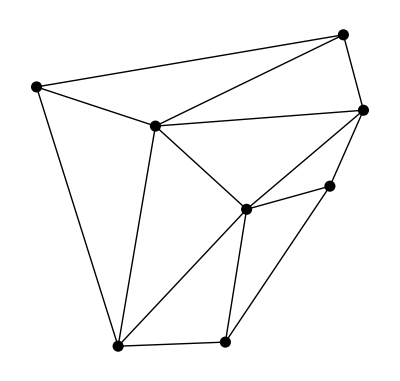

```mathematica
Pts2={{0.2664208421037788,8.048627792885714},{5.956903321073398,4.73087386414587},{5.382461346284593,1.1317010196187827},{3.48624996505432,6.986446756264407},{2.4761091263648094,1.0205380297971551},{8.213347291241853,5.358203413234129},{8.577916921870273,9.461213287784918},{9.122103023458276,7.416264188561708}};
n=Length[Pts2];
T=DelaunayTriangulation[Pts2];
TedgeI={};
For[i=1,i≤n,i++,TedgeI=Append[TedgeI,Sort[{i,#}]&/@T[[i,2]]] ]
Tedge=Flatten[TedgeI,1]//DeleteDuplicates;
Graphics[GraphicsComplex[Pts2,{PointSize[.02],Point[Range[n]],Line[Tedge](*,Text[Style[ToString[#],Large],#]&/@Range[n]*)}]]
```

```mathematica
Length[Tedge]
```

15

```mathematica
Triangles={{1,5,4},{1,4,7},{2,4,5},{2,5,3},{2,3,6},{2,6,8},{2,8,4},{4,7,8}};
Pts23D=Append[#,0]&/@Pts2;
Pts23D1=Pts23D;
Pts23D1[[1]]={0,0,3}+Pts23D[[1]];
Pts23D2=Pts23D;
Pts23D2[[2]]={0,0,3}+Pts23D[[2]];
Pts23D3=Pts23D;
Pts23D3[[3]]={0,0,3}+Pts23D[[3]];
Pts23D4=Pts23D;
Pts23D4[[4]]={0,0,3}+Pts23D[[4]];
Pts23D5=Pts23D;
Pts23D5[[5]]={0,0,3}+Pts23D[[5]];
Pts23D6=Pts23D;
Pts23D6[[6]]={0,0,3}+Pts23D[[6]];
Pts23D7=Pts23D;
Pts23D7[[7]]={0,0,3}+Pts23D[[7]];
Pts23D8=Pts23D;
Pts23D8[[8]]={0,0,3}+Pts23D[[8]];
Cpts=Join[Pts2[[#]],{Values[[#]]}]&/@Range[n];
DT3D=Graphics3D[GraphicsComplex[Pts23D,{PointSize[.02],Point[Range[n]],Line[Tedge]}],Boxed->False,Lighting->"Neutral"];
Graph1=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D1,{Polygon[Triangles]}]},Boxed->False,Lighting->"Neutral"];
Graph2=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D2,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
Graph3=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D3,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
Graph4=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D4,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
Graph5=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D5,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
Graph6=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D6,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
Graph7=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D7,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
Graph8=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Pts23D8,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
PointsPL=Graphics3D[{GraphicsComplex[Cpts,{PointSize[.02],Point[Range[n]]}]},Boxed->False,Lighting->"Neutral"];
IPoints=Graphics3D[{Opacity[0],GraphicsComplex[Cpts,{PointSize[.02],Point[Range[n]]}]},Boxed->False,Lighting->"Neutral"];
GraphPL=Graphics3D[{Gray,Opacity[.7],GraphicsComplex[Cpts,Polygon[Triangles]]},Boxed->False,Lighting->"Neutral"];
Show[DT3D,PointsPL,GraphPL]
```

-Graphics3D-

```mathematica
Values=RandomReal[{1,5},8];
Cpts=Join[Pts2[[#]],{Values[[#]]}]&/@Range[n]
```

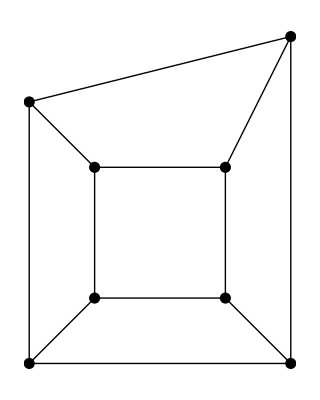

```mathematica
(*The Basics*)
k=25;
s=25;
vertin={{-1,-1},{-1,1},{1,1},{1,-1}};
vertout={{-2,-2},{-2,2},{2,2},{2,-2}};
vertout2={{-2,-2},{-2,2},{2,3},{2,-2}};
vert=Join[vertin,vertout];
vert2=Join[vertin,vertout2];
fs={{0,1,5,4},{1,2,6,5},{2,3,7,6},{0,3,7,4},{0,1,2,3}};
es={{0,1},{1,2},{2,3},{0,3},{0,4},{1,5},{2,6},{3,7},{4,5},{5,6},{6,7},{4,7}};
e2=es+1;
P0=Graphics[GraphicsComplex[vert,{Thick,Line[e2],PointSize[.02],Point[Range[8]](*Text[Style[ToString[#],20],#]&/@Range[8]*)}]];
P1=Graphics[Join[{Thick,Black,GraphicsComplex[vert,{Line[e2],PointSize[.02],Point[Range[8]]}]},{Text[Style["(-1,-1)",k],{-.7,-1.15}],Text[Style["(1,-1)",k],{.8,-1.15}],
Text[Style["(1,1)",k],{.85,1.15}],
Text[Style["(-1,1)",k],{-.7,1.15}],
Text[Style["(-2,-2)",k],{-2,-2.15}],
Text[Style["(2,-2)",k],{2,-2.15}],
Text[Style["(2,2)",k],{2,2.15}],
Text[Style["(-2,2)",k],{-2,2.15}]}]];
Labels=Graphics[{Text[Style["-1",s],{0,2.2}],Text[Style["-1",s],{2.2,0}],Text[Style["-1",s],{-2.2,0}],Text[Style["-1",s],{0,-2.2}],Text[Style["2",s],{.85,0}],Text[Style["2",s],{-.85,0}],Text[Style["2",s],{0,.85}],Text[Style["2",s],{0,-.85}],Text[Style["4",s],{1.4,1.6}],Text[Style["4",s],{-1.4,1.6}],Text[Style["4",s],{1.4,-1.6}],Text[Style["4",s],{-1.4,-1.6}]}];
P2=Graphics[Join[{Thick,Black,GraphicsComplex[vert2,{Line[e2],PointSize[.02],Point[Range[8]]}]},{Text[Style["(-1,-1)",k],{-.7,-1.15}],Text[Style["(1,-1)",k],{.8,-1.15}],
Text[Style["(1,1)",k],{.85,1.15}],
Text[Style["(-1,1)",k],{-.7,1.15}],
Text[Style["(-2,-2)",k],{-2,-2.15}],
Text[Style["(2,-2)",k],{2,-2.15}],
Text[Style["(2,3)",k],{2,3.15}],
Text[Style["(-2,2)",k],{-2,2.15}]}]];
P2NV=Graphics[{Thick,Black,GraphicsComplex[vert2,{Line[e2],PointSize[.02],Point[Range[8]]}]}];
Show[P2NV]
```

```mathematica
fs+1
```

{{1,2,6,5},{2,3,7,6},{3,4,8,7},{1,4,8,5},{1,2,3,4}}

```mathematica
Select[fs+1,Union[Sort[#],{1,2}]==Sort[#]&]
```

{{1,2,6,5},{1,2,3,4}}

```mathematica
Union[{1,2,6,5},{1,2}]
```

{1,2,5,6}

```mathematica
(*Polygonal PL function graphs and Maxwell's observation*)
k=1;
G[x_,y_]:=x;
vert3Dout=Append[#,0]&/@vertout;
vert3Dinup=Append[#,4]&/@vertin;
vert3Dindown=Append[#,0]&/@vertin;
base=Graphics3D[GraphicsComplex[Join[vert3Dindown,vert3Dout],{Line[e2],PointSize[.015],Point[Range[8]]}]];
base34=Graphics3D[GraphicsComplex[Join[vert3Dindown,vert3Dout],{Line[e2],PointSize[.015],Point[{3,4}],Thickness[.01],Black,Line[{3,4}]}]];
labels34=Graphics3D[{Text[Style["(1,1)",20],{1,1.6,0}],Text[Style["(1,-1)",20],{1,-1.6,0}],Text[Style["(0,0)",20],{0,.6,0}],Text[Style["(4,0)",20],{3.8,.6,0}],PointSize[.02],Point[{{0,0,0},{4,0,0},{1,1,0},{1,-1,0}}]}];
arrow34=Graphics3D[{Arrow[{{1,1,0},{1,-1,0}}],Arrow[{{4,0,0},{0,0,0}}]}];
graph=Graphics3D[GraphicsComplex[Join[vert3Dinup,vert3Dout],{FaceForm[Opacity[.6]],Gray,Polygon[fs+1]}],Boxed->False,Lighting->"Neutral"];
graph34=Graphics3D[GraphicsComplex[Join[vert3Dinup,vert3Dout],{FaceForm[Opacity[.6]],Polygon[Select[fs+1,Union[Sort[#],{3,4}]==Sort[#]&]]}]];
graphx=Graphics3D[{Opacity[1],Polygon[{{-2,-2,-k},{-2,2,-k},{2,2,k},{2,-2,k}}]}];
graphy=Graphics3D[{Opacity[1],Polygon[{{-2,-2,-k},{-2,2,k},{2,2,k},{2,-2,-k}}]}];
graph1=Graphics3D[{Opacity[0],Point[{0,0,-1}],Opacity[1],Polygon[{{-2,-2,1},{-2,2,1},{2,2,1},{2,-2,1}}]}];
normals=Append[{{0,0,0}},#]&/@{{2,0,1},{-2,0,1},{0,-2,1},{0,2,1},{0,0,1}};
basednormals=Graphics3D[{Arrow[Map[#-{0,0,1}&,normals,{2}]],Red,Arrow[BezierCurve[{{0,0,-1},{-.2,-.2,-.5},{0,0,0}}]]}];
basednormals34=Graphics3D[Arrow[{{{0,0,-1},{4,0,0}},{{0,0,-1},{0,0,0}}}]];
ibasednormals34=Graphics3D[{Opacity[0],Point[{{4,0,0},{0,0,-1}}]}];
normaline34=Graphics3D[{Thickness[.01],Line[{{4,0,0},{0,0,0}}]}];
planenormals=Graphics3D[{Arrow[{{{0,0,0},{0,0,1}},{{0,0,2},{0,0,3}},{{0,-1.5,1},{0,-3.5,2}},{{-1.5,0,1},{-3.5,0,2}},{{1.5,0,1},{3.5,0,2}},{{0,1.5,1},{0,3.5,2}}}],Red,Arrow[{{0,0,0},{0,0,1}}]}];
planenormals34=Graphics3D[Arrow[{{{1.5,0,2},{5.5,0,3}},{{0,0,4},{0,0,5}}}]];
inormals=Graphics3D[{Opacity[0],Point[{{0,0,3},{0,-3.5,2},{-3.5,0,2},{3.5,0,2},{0,3.5,2}}]}];
inormals34=Graphics3D[{Opacity[0],Point[{{0,0,5},{5.5,0,3}}]}];
rpoints={{0,0},{2,0},{0,2},{-2,0},{0,-2}};
rpoints1=Graphics3D[{Red,PointSize[.03],Point[{{0,0,0}}],Black,PointSize[.02],Point[Append[#,0]&/@rpoints]}];
redges={{1,2},{1,3},{1,4},{1,5},{2,3},{3,4},{4,5},{2,5}};

rgraph=Graphics3D[GraphicsComplex[Append[#,0]&/@rpoints,{Black,Thickness[.015],Line[redges],Black,PointSize[.02],Point[Range[5]],Thickness[.01],Red,BezierCurve[{1,{.5,.1,.2},2}],BezierCurve[{1,{-.5,.1,.2},4}],BezierCurve[{1,{.1,.5,.2},3}],BezierCurve[{1,{.1,-.5,.2},5}]}]];
e=Graphics3D[Text[Style["e",30],{.7,.2,0}]];
f=Graphics3D[Text[Style["e'",30],{2.4,0,0}]];
Show[{base78,graph78,planenormals78,f},Boxed->False]
```

-Graphics3D-

```mathematica
Show[graph,Graphics3D[GraphicsComplex[Join[vert3Dindown,vert3Dout],{Line[e2]}]]]
```

-Graphics3D-

```mathematica
Show[%1118,ViewPoint->Above]
```

-Graphics3D-

```mathematica
Show[%1027,ViewPoint->Above]
```

-Graphics3D-

```mathematica
GraphData["TruncatedCubicalGraph"]
```

-Graphics-

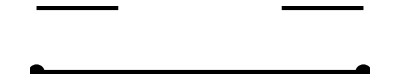

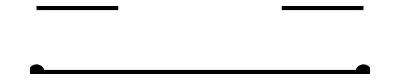

```mathematica
tension=Graphics[{Thickness[.01],Line[{{-1,0},{1,0}}],PointSize[.03],Point[{{-1,0},{1,0}}],Thickness[.01],Arrow[{{-1,.1},{-.5,.1}}],Thickness[.01],Arrow[{{1,.1},{.5,.1}}]}]
compression=Graphics[{Thickness[.01],Line[{{-1,0},{1,0}}],PointSize[.03],Black,Point[{{-1,0},{1,0}}],Thickness[.01],Arrow[{{-.5,.1},{-1,.1}}],Thickness[.01],Arrow[{{.5,.1},{1,.1}}]}]
```

```mathematica
Manipulate[Graphics3D[{Opacity[.5],FaceForm[Gray],EdgeForm[{Thickness[.005],Black}],PolyhedronData["TruncatedCube","Faces"]},Lighting->"Neutral",Boxed->False,ViewVector->{{0,3-d,0},{0,0,0}},ViewVertical->{1,0,0},ViewAngle->.6Pi],{d,0,Pi}]
```

```mathematica
Graphics3D[{Opacity[.5],FaceForm[Gray],EdgeForm[{Thickness[.005],Black}],PolyhedronData["TruncatedCube","Faces"]},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-